# Orthogonal faces of the quantum set in the CHSH scenario

## Preliminaries

We want to study the geometry of the quantum set of behaviors (correlations), which is convex. Specifically, we want to study the quantum set through the dual perspective. Since one can fully characterize a convex set in terms of its extremal points, it will be then sufficient to study orthogonal faces (faces of the dual).

One defines operators acting on the single-qubit space as

```mathematica
X=PauliMatrix[1];
Y=PauliMatrix[2];
Z=PauliMatrix[3];
I2=IdentityMatrix[2];
```

and operators acting on the 2-qubit space using the tensor product of single-qubit operators as

```mathematica
ZA=KroneckerProduct[Z,I2];
ZB=KroneckerProduct[I2,Z];
XA=KroneckerProduct[X,I2];
XB=KroneckerProduct[I2,X];
ZZ=KroneckerProduct[Z,Z];
XX=KroneckerProduct[X,X];
ZX=KroneckerProduct[Z,X];
XZ=KroneckerProduct[X,Z];
II=KroneckerProduct[I2,I2];
```

### General realization and behavior

Now, one considers the realization given by

```mathematica
phi[θ_]:= {Cos[θ],0,0,Sin[θ]};
$Assumptions=θ∈Reals&&a[0]∈Reals&&a[1]∈Reals&&b[0]∈Reals&&b[1]∈Reals;
A[i_]:=Cos[a[i]]ZA+Sin[a[i]]XA;
B[i_]:=Cos[b[i]]ZB+Sin[b[i]]XB;
```

Such implementation gives the following probability distribution (behavior)

```mathematica
(*Here, A and B are matrices*)
Ops={{II, B[0],B[1]},{A[0],A[0].B[0],A[0].B[1]},{A[1],A[1].B[0],A[1].B[1]}};
Pprime[θ_] := Flatten[
Table[FullSimplify[ConjugateTranspose[phi[θ]].Ops[[i,j]].phi[θ]],{i,1,3},{j,1,3}]
];
P[θ_]:=Drop[Pprime[θ],1];
P[θ]//MatrixForm
```

(Cos[2 θ] Cos[b[0]]
Cos[2 θ] Cos[b[1]]
Cos[2 θ] Cos[a[0]]
Cos[a[0]] Cos[b[0]]+Sin[2 θ] Sin[a[0]] Sin[b[0]]
Cos[a[0]] Cos[b[1]]+Sin[2 θ] Sin[a[0]] Sin[b[1]]
Cos[2 θ] Cos[a[1]]
Cos[a[1]] Cos[b[0]]+Sin[2 θ] Sin[a[1]] Sin[b[0]]
Cos[a[1]] Cos[b[1]]+Sin[2 θ] Sin[a[1]] Sin[b[1]])

The behavior is correct!

## Bell expression and Bell operator

### Background

- We want to characterize the quantum set via is dual
- That means that we want to characterize orthogonal faces of a given behavior.
- Characterizing orthogonal faces means to characterize Bell expressions.
- All possible Bell expressions for the (n=2, m=2, k=2) scenario can be parametrized by eight real coefficients:

BellExpression[A, B]  =  a[0] A[0] + a[1] A[1] + b[0] B[0] + b[1] B[1] + c[0, 0] A[0] B[0] + c[1, 0] A[1] B[0] + c[0, 1] A[0] B[1] + c[1, 1] A[1] B[1];

Be careful: the a[i], b[i] are not the same that appears in the measurement operators!!

- The Bell expression is related to the Bell operator by 

β.P = < ψ | S | ψ >. 

Given a Bell expression and a given realization, we can construct a Bell operator. In this specific case the Bell operator (induced by such a Bell expression and the considered realization, in terms of projectors) is

(*Matrices*)
S = p[1] ZA + p[2] XA + p[3] ZB + p[4] XB + p[5] ZZ + p[6] XX + p[7] ZX + p[8] XZ;

One can write the general Bell expression as a vector 

β := {b[0], b[1], a[0], c[0, 0], c[0, 1], a[1], c[1, 0], c[1, 1]};

### Conditions to restrict the Bell expression (no calculations)

We define a measurement vector of operators M,

M := {B[0],  B[1], A[0], A[0].B[0], A[0].B[1], A[1], A[1].B[0], A[1].B[1]}

- |ξ_i> is a vector of space orthogonal to |ϕ(θ)>
- T_i := <ξ_i|M|ϕ>
- |ϕ> is an eigenstate of S with maximum eigenvalue iff β.T_i = 0.

To find conditions on p[i]s, we first need a basis of the orthogonal of |ϕ(θ)>:

```mathematica
xi[1] =  {-Sin[θ],0,0,Cos[θ]};
xi[2] = {0,1,0,0};
xi[3] = {0, 0, 1, 0};
```

Recall that P = <ψ|M|ψ>, β.P = <ψ|β.M |ψ>, and S = β.M.

Then, we compute the vectors T_i for every ξ_i and impose β.T_i = 0. This condition comes from the fact that, if the behavior P that we want to characterize has to give a maximal quantum value (β_Q, a Tsirelson bound), then the state |ϕ(θ)> must be an eigenstate of the Bell operator of maximum eigenvalue. We have then four more conditions on the parametrization of the Bell operator. The parameter space is then five-d!

### The Nullifiers representation

We started with 8 p[i] parameters. Then, we find 3 conditions given by the orthogonal states to phi[\theta]. Then, knowing that phi[\theta] must be an eigenvector of S with eigenstate 1, and that the other vectors which are orthogonal to phi[\theta] must be annealed by S, we claim that the Bell operator must be of the form:

S = 1 + ∑_{k=1}^5 p_k N_k,

where the N_ks form a basis of nullifiers of \phi[\theta].

A basis of nullifiers for phi(\theta) is given by

```mathematica
Nullifiers={
ZA - ZB,II-ZZ,XZ+ZX-(1-Sin[2θ])/Cos[2θ](XA+XB),(1+Sin[2θ])(XA-XB)-Cos[2θ](XZ-ZX),II-Sin[2θ]XX-Cos[2θ]ZB
};
```

We verify that we are dealing with nullifiers:

```mathematica
Table[Nullifiers[[k]].phi[θ],{k,1,5}]//FullSimplify
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

It works! Achtung: they are not the same as in the cited paper! But they work!

Our analysis shows that conditions \beta.\vec{T}_i = 0 allows to write the Bell operator as

```mathematica
Sred:=II + Sum[p[k]Nullifiers[[k]],{k, 1,5}]
```

Note that the p[i] are different from the ones of the previous expansion of the Bell operator! To verify, we can determine

```mathematica
ConjugateTranspose[phi[θ]].Sred.phi[θ]//FullSimplify
```

1

As it must be!

### The reduced Bell expression

We now want to write the Bell expression related to the reduced Bell operator. We start by expanding Sred, thought as a formal polynomial expression

```mathematica
NullifiersFormal={
ZAA - ZBB,III-ZAA ZBB,XAA ZBB+ZAA XBB-(1-Sin[2θ])/Cos[2θ](XAA+XBB),(1+Sin[2θ])(XAA-XBB)-Cos[2θ](XAA ZBB-ZAA XBB),III-Sin[2θ]XAA XBB-Cos[2θ]ZBB
};
```

```mathematica
(*Formal indeterminates*)
SredFormal:=III + Sum[p[k]NullifiersFormal[[k]],{k, 1,5}]
```

Following Victor, let us write projectors in terms of measurement operators:

```mathematica
Clear[A,B];
projectors = Solve[{A[0]==Cos[a[0]]ZAA+Sin[a[0]]XAA,A[1]==Cos[a[1]]ZAA+Sin[a[1]]XAA,B[0]==Cos[b[0]]ZBB+Sin[b[0]]XBB,B[1]==Cos[b[1]]ZBB+Sin[b[1]]XBB},{XAA,XBB,ZAA,ZBB}][[1]]//FullSimplify
```

{XAA→(-A[1] Cos[a[0]]+A[0] Cos[a[1]]) Csc[a[0]-a[1]],XBB→(-B[1] Cos[b[0]]+B[0] Cos[b[1]]) Csc[b[0]-b[1]],ZAA→Csc[a[0]-a[1]] (A[1] Sin[a[0]]-A[0] Sin[a[1]]),ZBB→Csc[b[0]-b[1]] (B[1] Sin[b[0]]-B[0] Sin[b[1]])}

We substitute everything in the new expression of the Bell operator, SredFormal (which is parametrized in terms of the 5 p[i]s):

```mathematica
Bellexpr=SredFormal/.projectors//FullSimplify;
```

```mathematica
coeffList=Flatten[CoefficientList[Bellexpr,{A[0],A[1],B[0],B[1]}]]//FullSimplify;
```

The ordering used in the coefficientList function is:  
1   1, 
2   B[1], 
3   B[0], 
4   B[0]B[1], 
5   A[1], 
6   A[1]B[1],
7    A[1] B[0], 
8    ???, 
9    A[0], 
10  A[0]B[1], 
11  A[0]B[0], 
12  ???, 
13   A[0] A[1], 
??, ??, ??.

Then, putting the coefficients in the right ordering (B0, B1, A0, A0B0, A0B1, A1, A1B0, A1B1):

```mathematica
β:={coeffList[[3]],coeffList[[2]],coeffList[[9]],coeffList[[11]],coeffList[[10]],coeffList[[5]],coeffList[[7]],coeffList[[6]]}//FullSimplify;
β//MatrixForm
```

(Csc[b[0]-b[1]] ((p[1]+Cos[2 θ] p[5]) Sin[b[1]]-Cos[b[1]] (p[4] (1+Sin[2 θ])+p[3] (Sec[2 θ]-Tan[2 θ])))
Csc[b[0]-b[1]] (-((p[1]+Cos[2 θ] p[5]) Sin[b[0]])+Cos[b[0]] (p[4] (1+Sin[2 θ])+p[3] (Sec[2 θ]-Tan[2 θ])))
Csc[a[0]-a[1]] (-p[1] Sin[a[1]]+Cos[a[1]] (p[4] (1+Sin[2 θ])+p[3] (-Sec[2 θ]+Tan[2 θ])))
-Csc[a[0]-a[1]] Csc[b[0]-b[1]] (Cos[2 θ] p[4] Sin[a[1]-b[1]]+Sin[a[1]] (Cos[b[1]] p[3]+p[2] Sin[b[1]])+Cos[a[1]] (Cos[b[1]] p[5] Sin[2 θ]+p[3] Sin[b[1]]))
Csc[a[0]-a[1]] Csc[b[0]-b[1]] (Cos[2 θ] p[4] Sin[a[1]-b[0]]+Sin[a[1]] (Cos[b[0]] p[3]+p[2] Sin[b[0]])+Cos[a[1]] (Cos[b[0]] p[5] Sin[2 θ]+p[3] Sin[b[0]]))
Csc[a[0]-a[1]] (p[1] Sin[a[0]]-Cos[a[0]] (p[4] (1+Sin[2 θ])+p[3] (-Sec[2 θ]+Tan[2 θ])))
Csc[a[0]-a[1]] Csc[b[0]-b[1]] (Cos[2 θ] p[4] Sin[a[0]-b[1]]+Sin[a[0]] (Cos[b[1]] p[3]+p[2] Sin[b[1]])+Cos[a[0]] (Cos[b[1]] p[5] Sin[2 θ]+p[3] Sin[b[1]]))
-Csc[a[0]-a[1]] Csc[b[0]-b[1]] (Cos[2 θ] p[4] Sin[a[0]-b[0]]+Sin[a[0]] (Cos[b[0]] p[3]+p[2] Sin[b[0]])+Cos[a[0]] (Cos[b[0]] p[5] Sin[2 θ]+p[3] Sin[b[0]])))

From the fact that the general Bell expression does not consider the identity operator, we get the following linear constraint (coefficient of the identity operator in the expansion of the Bell operator in terms of measurement operators):

```mathematica
coeffList[[1]]==0
```

III (1+p[2]+p[5])==0

### Additional linear constraint

Since we want that the realization of interest verify 1 = β.P = <ϕ(θ)|S|ϕ(θ)>, we have an additional linear constraint! The constraint reads

```mathematica
1 == Transpose[β].P[θ]//FullSimplify
```

1+p[2]+p[5]==0

Up to now, everything is consistent!

## Variational method

### Variational conditions

Now we can use the fact that small variations around the point of interest should not increase the value of the Bell expression: This conditions give a set of two linear equations:

```mathematica
Clear[θ,a,b]
```

```mathematica
D1P[θ_]:=D[P[θ],a[0]];
D2P[θ_]:=D[P[θ],b[0]];
D3P[θ_]:=D[P[θ],a[1]];
D4P[θ_]:=D[P[θ],b[1]];
D5P[θ_]:=D[P[θ],θ];
```

```mathematica
eq1=Transpose[β].D1P[θ]==0;
eq2=Transpose[β].D2P[θ]==0;
eq3=Transpose[β].D3P[θ]==0;
eq4=Transpose[β].D4P[θ]==0;
eq5=Transpose[β].D5P[θ]==0;
```

```mathematica
expr1=eq1[[1]]//FullSimplify
```

1/2 Csc[a[0]-a[1]] (2 Sin[a[0]] (-Cos[a[1]] (p[3]+Cos[2 θ] p[4]) Sin[2 θ]+(Cos[2 θ] p[1]-p[2]) Sin[a[1]])-2 Cos[a[0]] Sin[2 θ] (Cos[a[1]] p[5] Sin[2 θ]+(p[3]+Cos[2 θ] p[4]) Sin[a[1]]))

```mathematica
expr2=eq2[[1]]//FullSimplify
```

1/2 (-Cot[b[0]-b[1]] (p[2]+p[5])+Csc[b[0]-b[1]] (Cos[b[0]+b[1]] (p[2]+Cos[4 θ] p[5])-2 Cos[2 θ] p[1] Sin[b[0]] Sin[b[1]]+(-2 p[3] Sin[2 θ]+p[4] Sin[4 θ]) Sin[b[0]+b[1]]))

```mathematica
expr3=eq3[[1]]//FullSimplify//Expand;
expr4=eq4[[1]]//FullSimplify//Expand;
expr5=eq5[[1]]//Simplify//Factor;
```

Now expressions 1 and 2 are compatible with the ones obtained by Victor!

### Tsirelson point

Focusing on the specific case of the Tsirelson point, the parameters are:

```mathematica
θ=π/4;
b[0]=0;
b[1]=π/2;
a[0]=π/4;
a[1]=-π/4;
```

Hence, the equations reduce to:

```mathematica
{expr1,expr2,expr3,expr4,expr5}//Simplify
```

{1/2 (p[2]-p[5]),p[3],1/2 (-p[2]+p[5]),-p[3],0}

```mathematica
{expr1,expr2}//Simplify
```

{1/2 (p[2]-p[5]),p[3]}

We successfully recover Victor’s equations!!

## Local bounds

Here we use the same convention adopted in the paper “Extremal Tsirelson Inequalities”.

### Local polytopes

```mathematica
Clear[θ,a,b];
b[0]=0;
b[1]=π/2;
a[0]=π/4;
a[1]=-π/4;
```

Hence, the equations reduce to:

```mathematica
{expr1,expr2,expr3,expr4,expr5}//Simplify
```

{1/2 (-Cos[2 θ] p[1]+p[2]-p[5] Sin[2 θ]^2),p[3] Sin[2 θ]-1/2 p[4] Sin[4 θ],1/2 (Cos[2 θ] p[1]-p[2]+p[5] Sin[2 θ]^2),(-p[3]+Cos[2 θ] p[4]) Sin[2 θ],0}

This means that we can re-parametrize everything in terms of p1 and p4:

```mathematica
p[5]=-1-p[2];
p[3]=Cos[2 θ] p[4];
p[2]=(-(Sin[2 θ])^2 +Cos[2 θ] p[1])/(1+(Sin[2θ])^2);
```

Formally, the set L of local behaviors is defined by the elements of P that can be written in the form

p(ab|xy) = ∫_Λ  dλ p(a|x,λ)p(b|y,λ).

We can rephrase the local model as follows. Let λ = (a0, a1, b0, b1) define an assignment of outputs a_x and b_y for each of the inputs x=0,1 and y=0,1. Let dλ ∈ L denote the corresponding deterministic behavior

d_λ(ab|xy) = 1 if a=a_x and b=b_y and 0 otherwise

There are k^{2m} = 16 possible output assignments and therefore 16 such local deterministic behaviors. A behavior p is local if and only if it can be written as a convex combination of these deterministic points. Hence, the set L is a polytope. The local deterministic behaviors d_\lambda correspond to the vertices.

Recall: we are working in the space dual to the behavior space (= the space of Bell expressions). In fact, we have a parametrized Bell expression, this time with 4 parameters (instead of 2, as in the Tsirelson case).

```mathematica
OpsL={{1, i,j},{k,i k,j k},{l,i l,j l}};
Lprime[i_,j_,k_,l_] = Table[FullSimplify[OpsL[[a,b]]],{a,1,3},{b,1,3}];
L[i_,j_,k_,l_]:=Drop[Flatten[Lprime[i,j,k,l] ],1];
L[i,j,k,l] //MatrixForm
```

(i
j
k
i k
j k
l
i l
j l)

The convex region of expressions β(r0, r1) with a local maximum smaller than 1 is thus given by all points (r0, r1) satisfying β.L <= 1.

```mathematica
ineqs:=Flatten[Table[Transpose[β].L[i,j,k,l]<=1,{i,{-1,1}},{j,{-1,1}},{k,{-1,1}},{l,{-1,1}}]];
```

We can consider different realizations, in order to reduce the number of parameters!

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

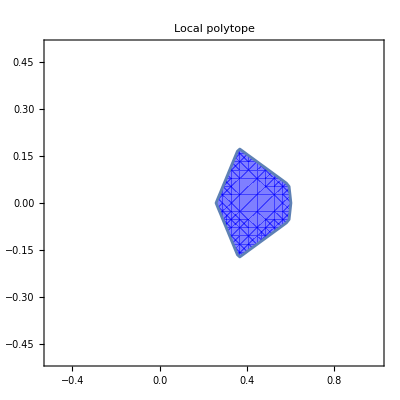
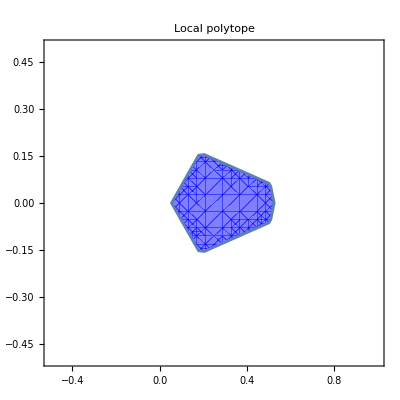
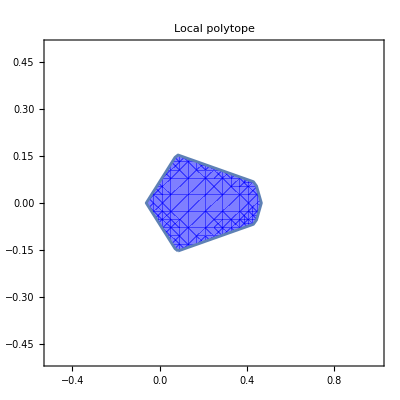
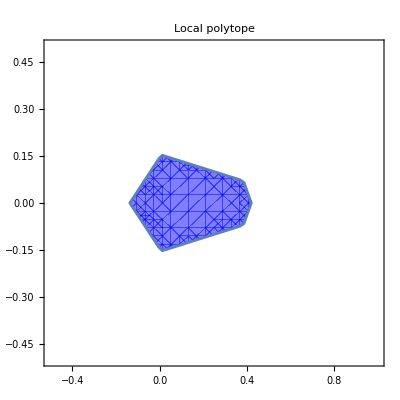
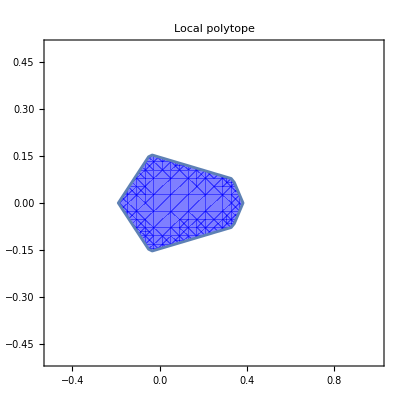
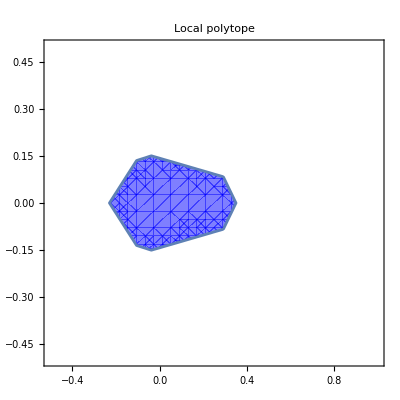
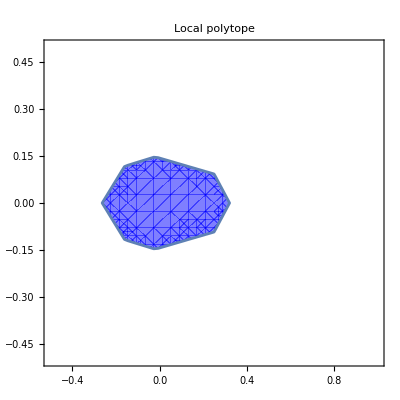
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[RegionPlot[Evaluate[And@@ineqs],{p[1],-0.5,1},{p[4],-0.5,0.5},
PlotStyle->Directive[Opacity[0.5],Blue],
PlotLabel->Style["Local polytope",Bold,16]],{θ, π/8+π/64, π/4, π/64}]
```

We notice the presence of a symmetry (p[4] -> - p[4]), probably due to the form of the Bell expression.

### Parametrized Bell expression

Let us see what is the form of the Bell expression parametrized by p1 and p4:

```mathematica
β //MatrixForm
```

(-(2 (Cos[2 θ]+(-1+Cos[4 θ]) p[1]))/(-3+Cos[4 θ])
-2 p[4]
(p[1]+2 p[4] Sin[2 θ])/(√2)
(-1+Cos[4 θ]+2 Cos[2 θ] p[1])/(√2 (-3+Cos[4 θ]))
((-5 Cos[2 θ]+Cos[6 θ]) p[4]-2 (1+Cos[2 θ] p[1]) Sin[2 θ])/(√2 (-3+Cos[4 θ]))
(p[1]-2 p[4] Sin[2 θ])/(√2)
(-1+Cos[4 θ]+2 Cos[2 θ] p[1])/(√2 (-3+Cos[4 θ]))
((-5 Cos[2 θ]+Cos[6 θ]) p[4]+2 Sin[2 θ]+p[1] Sin[4 θ])/(√2 (-3+Cos[4 θ])))

We can define a vector of measurements operators

```mathematica
M := {B[0],B[1],A[0],A[0].B[0], A[0].B[1],A[1],A[1].B[0],A[1].B[1]}
```

Then, the parametrized Bell expression than reads

```mathematica
Collect[Simplify[Transpose[β].M],{p[1],p[4]}]
```

-1/(2 (3-Cos[4 θ]))p[4] (-4 B[1] (-3+Cos[4 θ])+√2 (-5 Cos[2 θ]+Cos[6 θ]) A[0].B[1]+√2 (-5 Cos[2 θ]+Cos[6 θ]) A[1].B[1]+2 √2 A[0] (-3+Cos[4 θ]) Sin[2 θ]-2 √2 A[1] (-3+Cos[4 θ]) Sin[2 θ])-(-4 B[0] Cos[2 θ]-√2 A[0].B[0]+√2 Cos[4 θ] A[0].B[0]-√2 A[1].B[0]+√2 Cos[4 θ] A[1].B[0]-2 √2 A[0].B[1] Sin[2 θ]+2 √2 A[1].B[1] Sin[2 θ])/(2 (3-Cos[4 θ]))-1/(2 (3-Cos[4 θ]))p[1] (√2 A[0] (-3+Cos[4 θ])+√2 A[1] (-3+Cos[4 θ])-4 B[0] (-1+Cos[4 θ])+2 √2 Cos[2 θ] A[0].B[0]+2 √2 Cos[2 θ] A[1].B[0]-2 √2 Cos[2 θ] A[0].B[1] Sin[2 θ]+√2 A[1].B[1] Sin[4 θ])

With the Bell expression written in this form, we should be able to identify the symmetry!

```mathematica
Collect[Simplify[Transpose[β].M/.θ->π/4],{p[1],p[4]}]
```

1/4 (√2 A[0].B[0]+√2 A[0].B[1]+√2 A[1].B[0]-√2 A[1].B[1])+1/4 (2 √2 A[0]+2 √2 A[1]-4 B[0]) p[1]+1/4 (4 √2 A[0]-4 √2 A[1]-8 B[1]) p[4]

### Vertices as functions of θ

We have now inequalities parametrized by θ. To characterize the solution as a function of θ, it is sufficient to know the vertices, since the solution of the system of inequalities is given by the Convex Hull of the vertices, since we know that the local set L is a polytope! To find the vertices, it is sufficient to find all the intersections between the lines, that are characterized by the equations associated to the inequalities we have.

```mathematica
eqns:=ineqs/.LessEqual->Equal//FullSimplify;
```

We get all unique pairs of equations:

```mathematica
eqnPairs=Subsets[eqns,{2}];
```

We have 16 equations, so the possibilities are

```mathematica
Binomial[16,2]
```

120

Let’s check that everything works:

```mathematica
Length[eqnPairs]
```

120

We now try to solve the equations and find all the “candidates” for the vertices of the local polytopes

```mathematica
rawVertices=DeleteDuplicates[Select[Flatten[Table[Solve[pair,{p[1],p[4]},Reals],{pair,eqnPairs}],1],FreeQ[#,C[1]]&]]
```

There are 120 pairs of linear equations in p1 and p4, so we expect at most 120 solutions! Everything is working!

```mathematica
Length[rawVertices]
```

114

But the convex polytope is determined by very few points. How to exclude non-relevant solutions? Let’s try a different approach. We  guess that the vertices are always described by intersections of the same lines! Then, for a fixed θ, we can try to identify the correct sequence of lines that describe the vertices.

### What can we learn from the Tsirelson point case?

Which lines describe the vertices of the local polytope? For the Tsirelson behavior, the local polytope is given by

```mathematica
ineqsEval=ineqs/. θ->π/4;
(*Label each inequality so we can track where vertices come from*)
labeledIneqs=MapIndexed[#1->First[#2]&,ineqsEval];
(*Build all pairs of inequalities and their labels*)
labeledPairs=Subsets[labeledIneqs,{2}];
(*Go through each pair,solve,and check if solution lies in region*)
vertexData=Reap[Do[Module[{pair,eqs,sol},pair=pairEntry[[All,1]];
eqs=pair/. LessEqual->Equal;
sol=Quiet@Solve[eqs,{p[1],p[4]},Reals];
If[Length[sol]>0&&FreeQ[sol[[1]],C[1]]&&And@@(ineqsEval/. sol[[1]]),Sow[{pairEntry[[All,2]],sol[[1]]}]]],{pairEntry,labeledPairs}]][[2,1]];
```

```mathematica
vertexData//Table
```

{{{1,12},{p[1]→0,p[4]→1/4 (2-√2)}},{{1,15},{p[1]→-(3-2 √2)/(2 (-1+√2)),p[4]→-(-3+2 √2)/(4 (-1+√2))}},{{2,7},{p[1]→-(4-3 √2)/(2 (-1+√2)),p[4]→0}},{{2,16},{p[1]→-(-3+2 √2)/(2 (-1+√2)),p[4]→-(3-2 √2)/(4 (-1+√2))}},{{5,10},{p[1]→-(3-2 √2)/(2 (-1+√2)),p[4]→-(3-2 √2)/(4 (-1+√2))}},{{5,16},{p[1]→0,p[4]→1/4 (-2+√2)}},{{7,12},{p[1]→-(-3+2 √2)/(2 (-1+√2)),p[4]→-(-3+2 √2)/(4 (-1+√2))}},{{10,15},{p[1]→-(-4+3 √2)/(2 (-1+√2)),p[4]→0}}}

So, we got the list of lines describing the vertices! Then, we extract the data:

```mathematica
vertexCoords=vertexData[[All,2]];
contributingPairs=vertexData[[All,1]];
```

The couples of lines whose intersections describe the vertices of the dual local polytope for the Tsirelson behavior are

```mathematica
contributingPairs
```

{{1,12},{1,15},{2,7},{2,16},{5,10},{5,16},{7,12},{10,15}}

```mathematica
vertexCoords
```

{{p[1]→0,p[4]→1/4 (2-√2)},{p[1]→-(3-2 √2)/(2 (-1+√2)),p[4]→-(-3+2 √2)/(4 (-1+√2))},{p[1]→-(4-3 √2)/(2 (-1+√2)),p[4]→0},{p[1]→-(-3+2 √2)/(2 (-1+√2)),p[4]→-(3-2 √2)/(4 (-1+√2))},{p[1]→-(3-2 √2)/(2 (-1+√2)),p[4]→-(3-2 √2)/(4 (-1+√2))},{p[1]→0,p[4]→1/4 (-2+√2)},{p[1]→-(-3+2 √2)/(2 (-1+√2)),p[4]→-(-3+2 √2)/(4 (-1+√2))},{p[1]→-(-4+3 √2)/(2 (-1+√2)),p[4]→0}}

Now, consider the equations corresponding to these couples of lines in the partially entangled case. We can then recover some reasonable candidates for the vertices of the local polytopes in the general case:

```mathematica
vertexDataTheta = Table[Module[{eq1,eq2,sol},eq1=ineqs[[pair[[1]]]]/. LessEqual->Equal;
eq2=ineqs[[pair[[2]]]]/. LessEqual->Equal;
sol=Quiet@Solve[{eq1,eq2},{p[1],p[4]}];
pair->sol],{pair,contributingPairs}];
```

We then store the coordinates of this candidate in a vector v

```mathematica
v =Table[{p[1],p[4]}/.vertexDataTheta[[i,2, 1]],{i, 1, 8}];
```

For the Tsirelson point, we recover the known vertices:

```mathematica
v/.{θ->π/4}//FullSimplify
```

{{0,1/4 (2-√2)},{1/2-1/(√2),1/4 (-1+√2)},{1-1/(√2),0},{-1/2+1/(√2),1/4 (1-√2)},{1/2-1/(√2),1/4 (1-√2)},{0,1/4 (-2+√2)},{-1/2+1/(√2),1/4 (-1+√2)},{-1+1/(√2),0}}

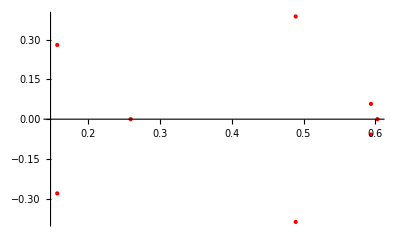
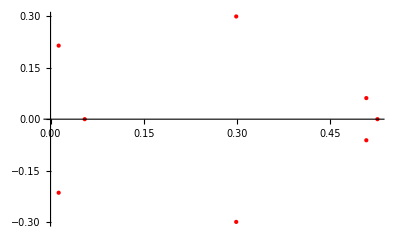
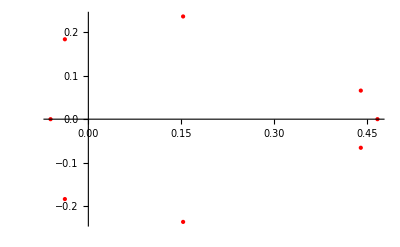
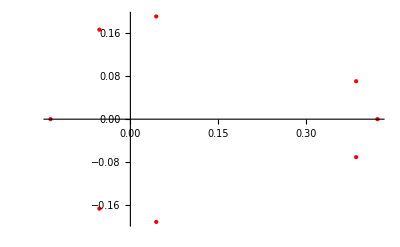
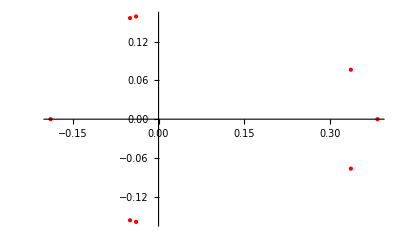
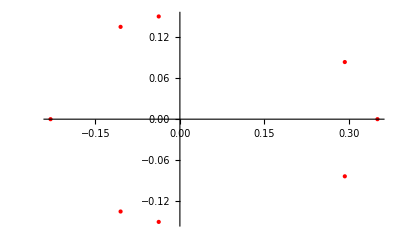
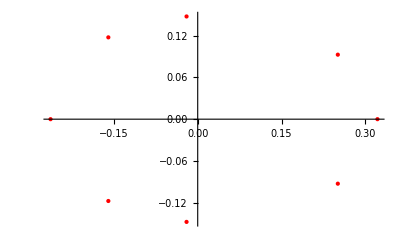
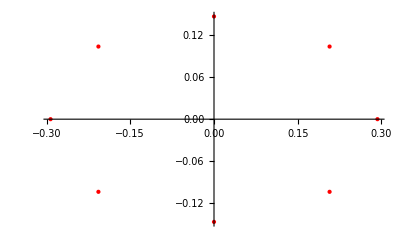

```mathematica
Table[ListPlot[v, PlotStyle->{Red,PointSize[Medium]}],{θ, π/8+π/64, π/4, π/64}]
```

Putting everything together, we verify if the considered points are good candidates for vertices:

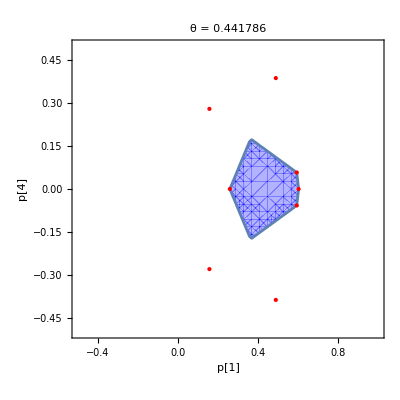
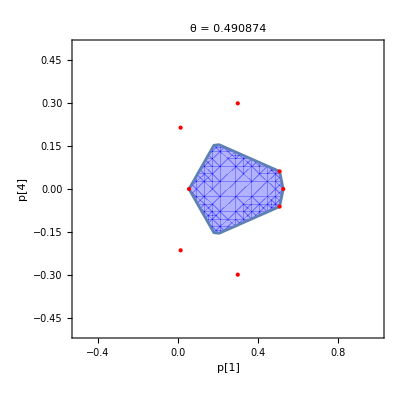
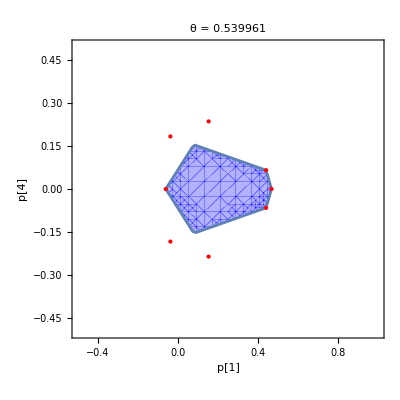
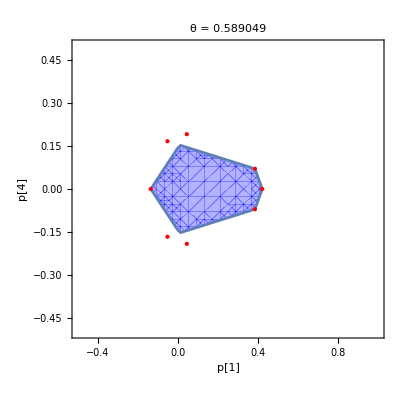
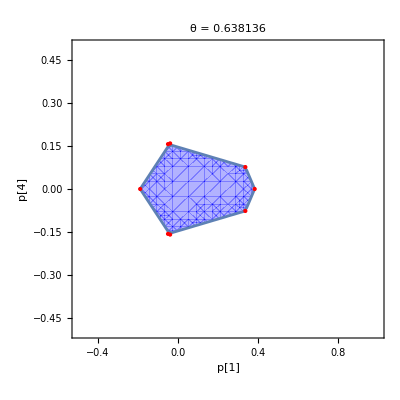
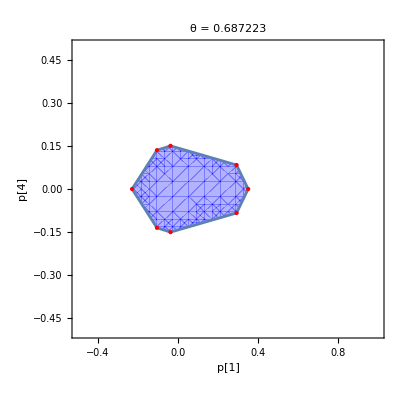
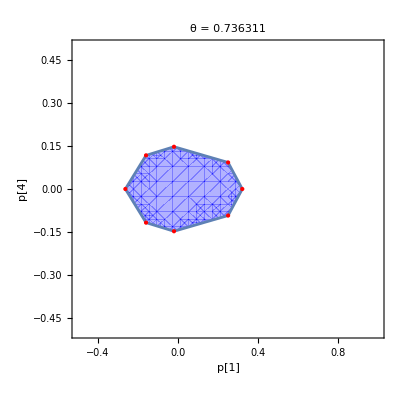
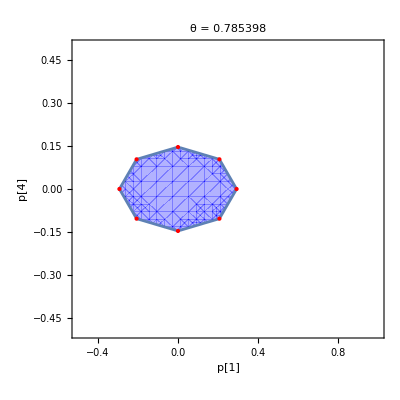

```mathematica
Table[Module[{region,vertexPlot},region=RegionPlot[Evaluate[And@@ineqs/. θ->th],{p[1],-0.5,1},{p[4],-0.5,0.5},PlotStyle->Directive[Opacity[0.3],Blue],AxesLabel->{Style["p[1]",Bold,14],Style["p[4]",Bold,14]},PlotLabel->Style["θ = "<>ToString[N[th]],Bold,16]];
vertexPlot=ListPlot[v/. θ->th,(*assuming v is a list of {p[1],p[4]} functions of θ*)PlotStyle->{Red,PointSize[Medium]},PlotRange->All];
Show[region,vertexPlot]],{th,π/8+π/64,π/4,π/64}]
```

### Understanding different regimes

Since our candidates are not always the vertices, we store all the 120 parametrized points in a vector:

```mathematica
coordFuncs=({p[1],p[4]}/. #)&/@rawVertices;
```

Let us try to study the situation in more detail:

```mathematica
thetaList=Range[π/8+π/64,π/4,π/2^10];

frames=Table[Module[{region,vertexPlot},region=RegionPlot[Evaluate[And@@(ineqs/. θ->th)],{p[1],-0.4,0.8},{p[4],-0.5,0.5},PlotStyle->Directive[Opacity[0.3],Blue],AxesLabel->{Style["p₁",Bold,14],Style["p₄",Bold,14]},PlotLabel->Style["θ = "<>ToString[N[th]],Bold,16]];
vertexPlot=ListPlot[v/. θ->th,PlotStyle->{Red,PointSize[Medium]},PlotRange->All];
Show[region,vertexPlot]],{th,thetaList}];
```

We can visualize the evolutions of these eight vertices:

```mathematica
Manipulate[Column[{frames[[i]],Row[{"θ = ",N[thetaList[[i]]]}]}],{{i,1,"Frame"},1,Length[frames],1}]
```

Part::partd: Part specification frames⟦113⟧ is longer than depth of object.

Part::partd: Part specification thetaList⟦113⟧ is longer than depth of object.

Part::partd: Part specification frames⟦113⟧ is longer than depth of object.

Part::partd: Part specification thetaList⟦113⟧ is longer than depth of object.

Part::partd: Part specification frames[[113]] is longer than depth of object.

Part::partd: Part specification thetaList[[113]]
     is longer than depth of object.

Part::partd: Part specification frames[[113]] is longer than depth of object.

Part::partd: Part specification thetaList[[113]]
     is longer than depth of object.

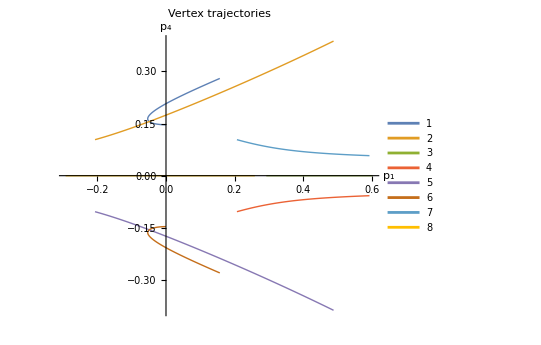

```mathematica
ParametricPlot[Evaluate[Table[v[[i]],{i,1,Length[v]}]/. θ->t],{t,π/8+π/64,π/4},PlotRange->All,AxesLabel->{Style["p₁",Bold,14],Style["p₄",Bold,14]},PlotLegends->Automatic,PlotStyle->Thick,PlotLabel->Style["Vertex trajectories",Bold,16]]
```

Now, we know that vertices 1, 2, 5, 6, do not work in all the regimes. But we need to individuate the missing vertices. To find new candidates, we consider the following:

```mathematica
ineqsN:=Flatten[Table[Transpose[β].L[i,j,k,l]<=1.001,{i,{-1,1}},{j,{-1,1}},{k,{-1,1}},{l,{-1,1}}]];
```

```mathematica
pointsAtTheta[θval_?NumericQ]:=(#/. θ->θval)&/@coordFuncs
```

```mathematica
verticesAtTheta[θval_?NumericQ]:=Module[{allPoints,ineqsEval},ineqsEval=ineqsN/. θ->θval;
allPoints=pointsAtTheta[θval];
Select[allPoints,Function[{pt},And@@Chop@N[ineqsEval/. {p[1]->pt[[1]],p[4]->pt[[2]]}]]]];
```

```mathematica
verticesAtTheta[π/8+π/16]//N
```

{{0.421218,0.},{0.384824,-0.0706813},{0.384824,0.0706813},{-0.136116,4.0465×10^-17},{0.00819441,-0.153281},{0.00819441,0.153281}}

As the Manipulate plot suggests, it seems like there are two regimes: the octagon regime and the hexagon regime. Now, we want to find the angle for which the regime change (which is probably the angle for which points 3 and 4 merge) and the missing vertices.

```mathematica
mergeq=v[[1,2]]==v[[2,2]]//FullSimplify
```

((4-3 √2) Sin[2 θ]^2)/(4-3 √2+√2 Cos[4 θ])==(2 Cos[θ] Sin[θ] ((-2+√2) Cos[θ]+(-4+3 √2) Sin[θ]))/(-3 √2 Cos[θ]+√2 Cos[5 θ]-3 (-2+√2) Sin[θ]+2 Sin[3 θ]+√2 Sin[5 θ])

```mathematica
FindInstance[mergeq&&θ∈Interval[{π/8+π/64,π/4}],θ,Reals]//N
```

FindInstance::ztest: Unable to decide whether numeric quantities {-741523456-524320768 √2+7377862656 √(2 (2210-1561 Power[«2»])) Cos[π/8]+3056009216 √(2 (2210-1561 Power[«2»])) Sin[π/8]+Root[1+Times[«2»]+Times[«2»]+Times[«2»]+Power[«2»]&,1,0]^2 (3829841920+2707980288 √2-38105071616 √(2 Plus[«2»]) Cos[π/8]-15783624704 √(2 Plus[«2»]) Sin[π/8])+Root[1+Times[«2»]+Times[«2»]+Times[«2»]+Power[«2»]&,1,0]^3 (3727818752+2635988992 √2-37091016704 √(2 Plus[«2»]) Cos[π/8]-15363604480 √(2 Plus[«2»]) Sin[π/8])+Root[1+4 Slot[«1»]-6 Power[«2»]-4 Power[«2»]+Slot[«1»]^4&,1,0] (-3113582592-2201583616 √2+30978998272 √(2 Plus[«2»]) Cos[π/8]+12831916032 √(2 Plus[«2»]) Sin[π/8]),«1»} are equal to zero. Assuming they are.

{{θ→{0.64454}}}

This is the angle that discriminates between the two regimes.

```mathematica
θT = 0.644539533
```

0.64454

### Vertices

Finally, we want to find the missing vertices: we can use the same method used for the

```mathematica
ineqsEval2=ineqs/. θ->0.589;

(*Label each inequality so we can track where vertices come from*)
labeledIneqs2=MapIndexed[#1->First[#2]&,ineqsEval2];

(*Build all pairs of inequalities and their labels*)
labeledPairs2=Subsets[labeledIneqs2,{2}];

(*Go through each pair,solve,and check if solution lies in region*)
vertexData2=Reap[Do[Module[{pair,eqs,sol},pair=pairEntry[[All,1]];
eqs=pair/. LessEqual->Equal;
sol=Quiet@Solve[eqs,{p[1],p[4]},Reals];
If[Length[sol]>0&&FreeQ[sol[[1]],C[1]]&&And@@(ineqsEval2/. sol[[1]]),Sow[{pairEntry[[All,2]],sol[[1]]}]]],{pairEntry,labeledPairs2}]][[2,1]];
```

```mathematica
vertexData2
```

{{{2,7},{p[1]→0.421259,p[4]→0.}},{{2,16},{p[1]→0.384875,p[4]→-0.0706759}},{{7,12},{p[1]→0.384875,p[4]→0.0706759}},{{10,15},{p[1]→-0.136055,p[4]→0.}},{{10,16},{p[1]→0.00825328,p[4]→-0.153281}},{{12,15},{p[1]→0.00825328,p[4]→0.153281}}}

We obtained six vertices! It seems it worked! Now, comparing with the other regime,

```mathematica
vertexData
```

{{{1,12},{p[1]→0,p[4]→1/4 (2-√2)}},{{1,15},{p[1]→-(3-2 √2)/(2 (-1+√2)),p[4]→-(-3+2 √2)/(4 (-1+√2))}},{{2,7},{p[1]→-(4-3 √2)/(2 (-1+√2)),p[4]→0}},{{2,16},{p[1]→-(-3+2 √2)/(2 (-1+√2)),p[4]→-(3-2 √2)/(4 (-1+√2))}},{{5,10},{p[1]→-(3-2 √2)/(2 (-1+√2)),p[4]→-(3-2 √2)/(4 (-1+√2))}},{{5,16},{p[1]→0,p[4]→1/4 (-2+√2)}},{{7,12},{p[1]→-(-3+2 √2)/(2 (-1+√2)),p[4]→-(-3+2 √2)/(4 (-1+√2))}},{{10,15},{p[1]→-(-4+3 √2)/(2 (-1+√2)),p[4]→0}}}

The missing vertices is given by the couple  {10, 16} and {12, 15}! We store the vertices in the new regime in a vector:

```mathematica
vertexCoords2=vertexData2[[All,2]];
contributingPairs2=vertexData2[[All,1]];
```

```mathematica
contributingPairs2
```

{{2,7},{2,16},{7,12},{10,15},{10,16},{12,15}}

```mathematica
vertexsols2 = Table[Module[{eq1,eq2,sol},eq1=ineqs[[pair[[1]]]]/. LessEqual->Equal;
eq2=ineqs[[pair[[2]]]]/. LessEqual->Equal;
sol=Quiet@Solve[{eq1,eq2},{p[1],p[4]}];
pair->sol],{pair,contributingPairs2}];
```

```mathematica
v2 =Table[{p[1],p[4]}/.vertexsols2[[i,2, 1]],{i, 1, 6}];
```

Basically, we are done! To verify that we are in the right direction, we plot the graphs for the new regime!

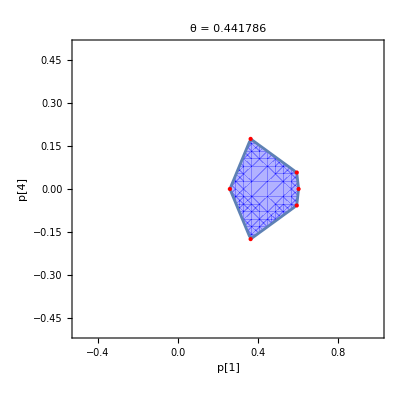
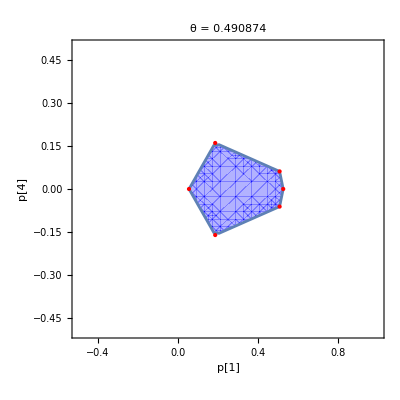
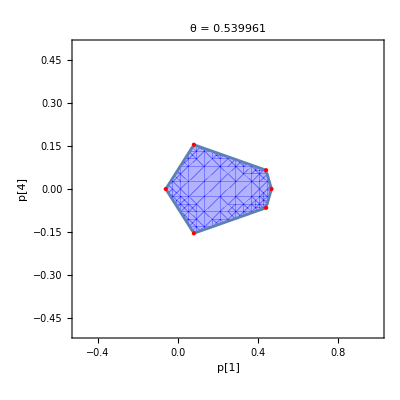
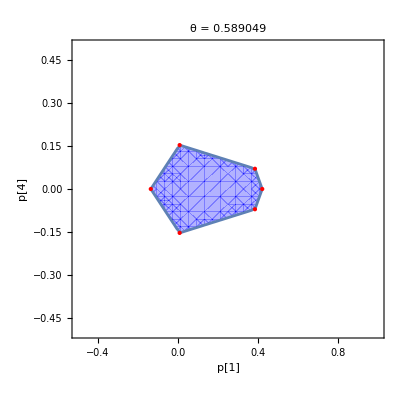
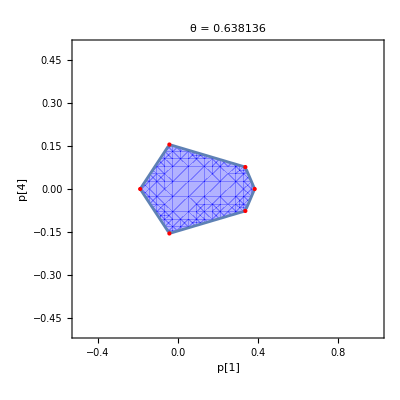
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
frames2 = Table[Module[{region,vertexPlot,verts},
(*Choose the correct vertex list based on theta*)
verts=If[th>θT,v,v2];
(*Plot the region*)
region=RegionPlot[Evaluate[And@@ineqs/. θ->th],{p[1],-0.5,1},{p[4],-0.5,0.5},PlotStyle->Directive[Opacity[0.3],Blue],AxesLabel->{Style["p[1]",Bold,14],Style["p[4]",Bold,14]},PlotLabel->Style["θ = "<>ToString[N[th]],Bold,16]];
(*Plot the vertices*)
vertexPlot=ListPlot[verts/. θ->th,PlotStyle->{Red,PointSize[Medium]},PlotRange->All];
Show[region,vertexPlot]],{th,π/8+π/64,π/4,π/64}]
```

```mathematica
Export["/Users/andrea/MEGAsync/Uni/PhysMSc/QStatistics/Notebooks/Orthogonal/Local_Polytopes.png",GraphicsGrid[Partition[frames2,4]]]
```

/Users/andrea/MEGAsync/Uni/PhysMSc/QStatistics/Notebooks/Orthogonal/Local_Polytopes.png

Finally, we want to extract the coordinates of the vertices for every considered value of theta.

```mathematica
vertexCoordsPerTheta=Table[Module[{verts},
verts=If[th>θT,v,v2];
verts/. θ->th],{th,π/8+π/64,π/4,π/64}];
```

```mathematica
vertexCoordsPerTheta//N
```

{{{0.602949,0.},{0.593874,-0.0575582},{0.593874,0.0575582},{0.259286,0.},{0.363104,-0.174863},{0.363104,0.174863}},{{0.526058,0.},{0.508129,-0.0613573},{0.508129,0.0613573},{0.0549822,0.},{0.186038,-0.160678},{0.186038,0.160678}},{{0.467438,0.},{0.440508,-0.0656677},{0.440508,0.0656677},{-0.0611424,0.},{0.0793299,-0.154632},{0.0793299,0.154632}},{{0.421218,0.},{0.384824,-0.0706813},{0.384824,0.0706813},{-0.136116,0.},{0.00819441,-0.153281},{0.00819441,0.153281}},{{0.383354,0.},{0.336718,-0.0766283},{0.336718,0.0766283},{-0.189162,0.},{-0.0431111,-0.15521},{-0.0431111,0.15521}},{{-0.0375969,0.150662},{-0.105336,0.135418},{0.350876,0.},{0.29288,-0.0838025},{-0.105336,-0.135418},{-0.0375969,-0.150662},{0.29288,0.0838025},{-0.229731,0.}},{{-0.0199615,0.147458},{-0.159806,0.117448},{0.321421,0.},{0.250543,-0.0925966},{-0.159806,-0.117448},{-0.0199615,-0.147458},{0.250543,0.0925966},{-0.263166,0.}},{{0.,0.146447},{-0.207107,0.103553},{0.292893,0.},{0.207107,-0.103553},{-0.207107,-0.103553},{0.,-0.146447},{0.207107,0.103553},{-0.292893,0.}}}

Maybe this format is also useful:

```mathematica
vertexCoordsWithTheta=N[Table[Module[{verts,currentVerts},
verts=If[th>θT,v,v2];
currentVerts=verts/. θ->th;
currentVerts=currentVerts/. {x_,y_}:>{x,2 y};{N[th],currentVerts}],{th,π/8+π/64,π/4,π/64}]];
```

```mathematica
vertexCoordsWithTheta
```

{{0.441786,{{0.602949,0.},{0.593874,-0.115116},{0.593874,0.115116},{0.259286,0.},{0.363104,-0.349725},{0.363104,0.349725}}},{0.490874,{{0.526058,0.},{0.508129,-0.122715},{0.508129,0.122715},{0.0549822,0.},{0.186038,-0.321356},{0.186038,0.321356}}},{0.539961,{{0.467438,0.},{0.440508,-0.131335},{0.440508,0.131335},{-0.0611424,0.},{0.0793299,-0.309264},{0.0793299,0.309264}}},{0.589049,{{0.421218,0.},{0.384824,-0.141363},{0.384824,0.141363},{-0.136116,0.},{0.00819441,-0.306563},{0.00819441,0.306563}}},{0.638136,{{0.383354,0.},{0.336718,-0.153257},{0.336718,0.153257},{-0.189162,0.},{-0.0431111,-0.310419},{-0.0431111,0.310419}}},{0.687223,{{-0.0375969,0.301323},{-0.105336,0.270836},{0.350876,0.},{0.29288,-0.167605},{-0.105336,-0.270836},{-0.0375969,-0.301323},{0.29288,0.167605},{-0.229731,0.}}},{0.736311,{{-0.0199615,0.294916},{-0.159806,0.234896},{0.321421,0.},{0.250543,-0.185193},{-0.159806,-0.234896},{-0.0199615,-0.294916},{0.250543,0.185193},{-0.263166,0.}}},{0.785398,{{0.,0.292893},{-0.207107,0.207107},{0.292893,0.},{0.207107,-0.207107},{-0.207107,-0.207107},{0.,-0.292893},{0.207107,0.207107},{-0.292893,0.}}}}

```mathematica
Export["/Users/andrea/MEGAsync/Uni/PhysMSc/QStatistics/Notebooks/Orthogonal/vertexCoords.json",vertexCoordsWithTheta]
```

/Users/andrea/MEGAsync/Uni/PhysMSc/QStatistics/Notebooks/Orthogonal/vertexCoords.json

### Recovering Victor’s Bell expression

```mathematica
BellT=Transpose[β].M /.θ->π/4//FullSimplify
```

1/4 (√2 A[0].B[0]+√2 A[0].B[1]+√2 A[1].B[0]-√2 A[1].B[1]-4 B[0] p[1]+2 √2 A[1] (p[1]-2 p[4])-8 B[1] p[4]+2 √2 A[0] (p[1]+2 p[4]))

```mathematica
Collect[BellT, {p[1],p[4]}]
```

1/4 (√2 A[0].B[0]+√2 A[0].B[1]+√2 A[1].B[0]-√2 A[1].B[1])+1/4 (2 √2 A[0]+2 √2 A[1]-4 B[0]) p[1]+1/4 (4 √2 A[0]-4 √2 A[1]-8 B[1]) p[4]

This is exactly Victor’s Bell expression, with p1 = r0 and p4 = 1/2r1!

## SOS Decomposition

We now want to find an SOS decomposition for some of the vertices of the local/quantum dual polytope. First, we look at vertex 3, since for this vertex p[4] = 0, and the Bell expression is way easier. We already have an ansatz for an SOS decomposition, since we know at least that in the θ = π/4 case, we have the SOS decomposition that Victor found.

```mathematica
Collect[FullSimplify[Transpose[β].M],{p[1],p[4]}]
```

-1/(2 (3-Cos[4 θ]))p[4] (-4 B[1] (-3+Cos[4 θ])+√2 (-5 Cos[2 θ]+Cos[6 θ]) A[0].B[1]+√2 (-5 Cos[2 θ]+Cos[6 θ]) A[1].B[1]+2 √2 A[0] (-3+Cos[4 θ]) Sin[2 θ]-2 √2 A[1] (-3+Cos[4 θ]) Sin[2 θ])-(-4 B[0] Cos[2 θ]-√2 A[0].B[0]+√2 Cos[4 θ] A[0].B[0]-√2 A[1].B[0]+√2 Cos[4 θ] A[1].B[0]-2 √2 A[0].B[1] Sin[2 θ]+2 √2 A[1].B[1] Sin[2 θ])/(2 (3-Cos[4 θ]))-1/(2 (3-Cos[4 θ]))p[1] (√2 A[0] (-3+Cos[4 θ])+√2 A[1] (-3+Cos[4 θ])-4 B[0] (-1+Cos[4 θ])+2 √2 Cos[2 θ] A[0].B[0]+2 √2 Cos[2 θ] A[1].B[0]-2 √2 Cos[2 θ] A[0].B[1] Sin[2 θ]+√2 A[1].B[1] Sin[4 θ])

### Interesting vertices

The interesting vertex, that can be already reached with the level  of the hierarchy is the 8th

```mathematica
v[[8]]//FullSimplify
```

{((√2-Csc[2 θ]) Sin[θ] (2 √2 Cos[θ]-3 Sin[θ]-Sin[3 θ]))/(√2 Cos[2 θ]+8 Cos[θ]^2 Sin[θ] (-Cos[θ]+√2 Sin[θ])),0}

```mathematica
v[[8]]/.θ->π/4//FullSimplify
```

{-1+1/(√2),0}

The other interesting vertex is the 3rd one

```mathematica
v[[3]]//FullSimplify
```

{(Cos[θ] Csc[2 θ] (-3 Cos[θ]+Cos[3 θ]+2 √2 Sin[θ]) (-1+√2 Sin[2 θ]))/(√2 Cos[2 θ]+8 Cos[θ] Sin[θ]^2 (-√2 Cos[θ]+Sin[θ])),0}

```mathematica
v[[3]]/.θ->π/4//FullSimplify
```

{1-1/(√2),0}